## Week 8 - Lecture 1: Random Walks

Resources  --  Video  &&  Notes 8a

Check pages 3-4 for basics of 1D discrete random walk.
Check pages 5-6 for calculating mean & variance of right-side movement.
Check page 7 for mean & variance of net displacement.
Check page 8 for unbiased random walk and its analytical solution. 
To derive PN(m) using Stirling's approximation, check this.

Note: If you take N steps and move by:
• O(N) - Ballistic motion
• O(√N) - Diffusive motion

## Week 8 - Lecture 2: Diffusion Equation & Random Walks

Resources  --  Video  &&  Notes 8b

In this lecture, we will see how to connect the random walks to the diffusion equation (Check pages 3-4)

```mathematica
p[x_, t_] = Exp[-x^2/t]/Sqrt[π t] (* Solution for diffusion equation with D=1/4 *)
```

(ⅇ^(-x^2/t))/(√π √t)

```mathematica
Manipulate[Plot[p[x,t], {x,-10,10}, PlotRange->All, AxesLabel->Automatic], {{t,10},0,100}]
```

In general, we see that the variance is proportional to 't' (or no. of steps), which is a characteristic of diffusive motion.

## Week 8 - Lecture 3: Numerical Simulation of Random Walks

Resources  --  Video  &&  Notes 8c

#### Generating an unbiased random walk

```mathematica
a={0};
Do[
AppendTo[a, a[[n-1]]+RandomChoice[{-1,1}]],
{n,2,500}]
ListPlot[a, Joined->True]
```

-Graphics-

#### Variance of unbiased RW

Now let us see if σ^2 = N for such a RW with mean <m> = 0.

```mathematica
data = Table[
variance=Mean[Table[
Total[Table[RandomChoice[{-1,1}], {n}]], (* Calculate m *)
{10000}]^2 // N]; (* Calculate m^2 many times & compute <m^2> *)
{n, variance}, {n,100,1000,100}]; (* 'n' is the number of steps N *)
```

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[x, {x,0,1500}]]
```

-Graphics-

#### PN(m) for unbiased RW

Let's check if PN(m) follows a normal distribution (like our analytical solution which was a Gaussian)

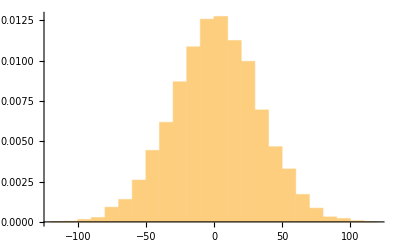

```mathematica
nMax = 1000; (* Fixed number of steps *)
binsize = 10;
histdata = Histogram[Table[
Total[Table[RandomChoice[{-1,1}], {nMax}]], (* Compute m *)
{10000}], {binsize}, "PDF"] (* Generate large no. of m's, and normalize them to get PDF*)
```

```mathematica
unbiasedsoln[x_, N_] = Exp[-x^2/(2N)]/Sqrt[2π N]
```

(ⅇ^(-x^2/(2 N)))/(√N √(2 π))

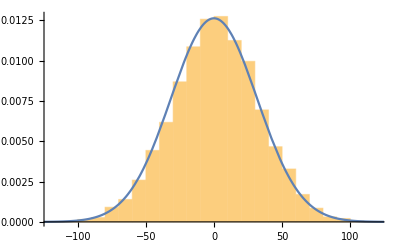

```mathematica
Show[histdata, 
Plot[unbiasedsoln[x,nMax], {x, -5√nMax, 5 √nMax}]]
```

#### Biased RW with probability 'p' for right step

```mathematica
p=0.55;
a={0};
Do[
AppendTo[a,a[[n-1]]+ (1-2 UnitStep[RandomReal[]-p])],
{n,2,500}];
ListPlot[a, Joined->True]
```

-Graphics-

We see that it drifts from the origin at a rate ∝ (p-q)

Now we will show that the biased random walk has <m^2> = N(N-1)(2p-1)^2:

```mathematica
msquared[n_] = n*(n-1)*(2p -1)^2;
data = Table[
variance=Mean[Table[
Total[Table[1-2 UnitStep[RandomReal[]-p], {n}]], (* Calculate m *)
{10000}]^2 // N]; (* Calculate m^2 many times & compute <m^2> *)
{n, variance}, {n,1000,10000,1000}]; (* 'n' is the number of steps N *)
Show[ListPlot[data, PlotStyle->Red], Plot[msquared[x], {x,0,15000}]]
```

-Graphics-

#### PN(m) for biased RW

Let us verify if the probability distribution for biased RW matches the analytical solution.

Assuming it will also be a Gaussian, we know that for biased RW,
<m> = 2N(p-0.5)  &&  σ^2 = 4Npq  (see lecture 1).
Hence substituting this in an 1D Gaussian,

```mathematica
p=0.55;
q=1-p;
biasedsoln[m_, N_] = Exp[-(m - (2N(p-0.5)))^2/(8N p q)]/Sqrt[8π N p q];
```

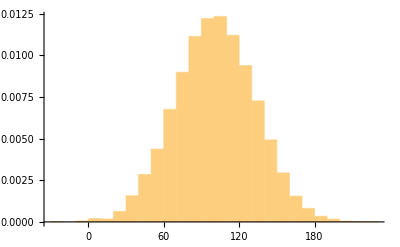

```mathematica
nMax = 1000; (* Fixed number of steps *)
binsize = 10;
histdata = Histogram[Table[
Total[Table[1-2 UnitStep[RandomReal[]-p], {nMax}]], (* Compute m *)
{10000}], {binsize}, "PDF"] (* Generate large no. of m's, and normalize them to get PDF*)
```

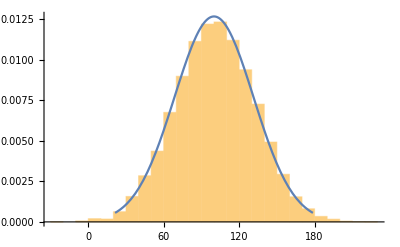

```mathematica
Show[histdata, 
Plot[biasedsoln[x,nMax], {x, 2nMax(p-0.5)-5√(nMax p q),2nMax(p-0.5)+ 5 √(nMax p q)}]]
```